```mathematica
(*(ccdata[7]/.{x_,y_}/;x>maxyx->{x,0})[[All,2]]*)
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define BWs

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;
```

## Charmonium

### Import Data

```mathematica
Tscanc=IntegerPart[1000 Table[i,{i,0.15,0.25,0.003}]]
```

{150,153,156,159,162,164,167,170,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,224,227,230,234,237,240,243,246,249}

```mathematica
Do[ccdata[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"spectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdata[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatau[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"uspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatau[n],Joined->True],{n,1,Length[Tscanc],1}]
```

```mathematica
Do[ccdatal[n]=Import["spectraldata/Tscan/cc/swccT"<>ToString[Tscanc[[n]]]<>"lspectra.dat"];,{n,Length[Tscanc]}];
Manipulate[ListPlot[ccdatal[n],Joined->True],{n,1,Length[Tscanc],1}]
```

### Fitting

```mathematica
fit[input_,output_]:=Module[{temp=Range[1,Length[Tscanc]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
bad={};
Do[If[maxys[[i]]<maxys[[i+1]],bad=Append[bad,i]],{i,Length[maxys]-1}]
Do[maxxs=Delete[maxxs,bad[[i]]];maxys=Delete[maxys,bad[[i]]];maxxis=Delete[maxxis,bad[[i]]];,{i,Length[bad]}]
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
Do[If[Or[2 input[n][[hwhmi[[-i]],2]]≤0.5 maxys[[-i]],2 input[n][[hwhmi[[-i]],2]]≥1.5 maxys[[-i]]],hwhmi[[-i]]=maxxis[[-i]]],{i,Length[hwhmi]-1}];
bad=Position[maxxis-hwhmi,0];
hwhmi=DeleteCases[maxxis-hwhmi,0];
maxxis=Delete[maxxis,bad];
maxxs=Delete[maxxs,bad];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[maxxis[[i]]-hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[mins[[i]];;mins[[i+1]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w],{i,Length[hwhmi]}];,{ii,Length[Tscanc]}];output=temp;]
```

```mathematica
fit[ccdata,ccmodel];
fit[ccdatau,ccmodelu];
```

```mathematica
Clear[ccmodell]
```

```mathematica
fit[ccdatal,ccmodell];
```

```mathematica
ccmodell[[6]]
```

{FittedModel[0.0157257+0.00109828/(0.0000424596+(-3.0795+w)^2)+0.0314985 (-3.0795+w)+(0.00340532 (-3.0795+w))/(0.0000424596+(-3.0795+w)^2)],FittedModel[0.49152+(2.73399×10^-8)/(5.44239×10^-13+(-3.56014+w)^2)+1.09412 (-3.56014+w)+(0.0000211113 (-3.56014+w))/(5.44239×10^-13+(-3.56014+w)^2)]}

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];
If[Length[ccmodel[[i]]]>1,ccTcut=i];If[Length[ccmodelu[[i]]]>1,ccTucut=i];If[Length[ccmodell[[i]]]>1,ccTlcut=i];,{i,Length[ccmodel]}];
```

```mathematica
ccTcut
```

17

```mathematica
ccTucut
```

9

```mathematica
ccTlcut
```

29

```mathematica
Γfitccl
```

{{0.00432195,0.0263501},{0.00585432,0.0353069},{0.00755602,0.0450247},{0.00925653,0.055166},{0.0111077,0.0658616},{0.0130322,1.47545×10^-6},{0.0150515,0.0814632},{0.0174265,0.0948896},{0.0191538,0.108877},{0.0211136,0.123777},{0.0236629,0.139849},{0.0259878,0.155971},{0.0283803,0.172184},{0.030816,6.67688×10^-7},{0.0333077,0.204039},{0.0358609,0.219308},{0.038452,0.233868},{0.0411259,0.247579},{0.0437248,0.260135},{0.0462428,0.271357},{0.0489936,0.281711},{0.0515988,0.291095},{0.0544345,0.299689},{0.0572238,0.308134},{0.0600613,0.318024},{0.0629294,0.327794},{0.0658565,0.337733},{0.0688577,0.347185},{0.0717855,0.356517},{},{},{},{},{}}

```mathematica
wrfitcc=Range[Length[ccmodel]];
Do[wrfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[wrfitcc[[i,ii]]=wr/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[wrfitcc[[i]]]}],{i,Length[wrfitcc]}]

wrfitccu=Range[Length[ccmodelu]];
Do[wrfitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[wrfitccu[[i,ii]]=wr/.ccmodelu[[i,ii]]["BestFitParameters"],{ii,Length[wrfitccu[[i]]]}],{i,Length[wrfitccu]}]

wrfitccl=Range[Length[ccmodell]];
Do[wrfitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[wrfitccl[[i,ii]]=wr/.ccmodell[[i,ii]]["BestFitParameters"],{ii,Length[wrfitccl[[i]]]}],{i,Length[wrfitccl]}]

Γfitcc=Range[Length[ccmodel]];
Do[Γfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[Γfitcc[[i,ii]]=Γ/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[Γfitcc[[i]]]}],{i,Length[Γfitcc]}]

Γfitccu=Range[Length[ccmodelu]];
Do[Γfitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[Γfitccu[[i,ii]]=Γ/.ccmodelu[[i,ii]]["BestFitParameters"],{ii,Length[Γfitccu[[i]]]}],{i,Length[Γfitccu]}]

Γfitccl=Range[Length[ccmodell]];
Do[Γfitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[Γfitccl[[i,ii]]=Γ/.ccmodell[[i,ii]]["BestFitParameters"],{ii,Length[Γfitccl[[i]]]}],{i,Length[Γfitccl]}]

constfitcc=Range[Length[ccmodel]];
Do[constfitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[constfitcc[[i,ii]]=const/.ccmodel[[i,ii]]["BestFitParameters"],{ii,Length[constfitcc[[i]]]}],{i,Length[constfitcc]}]

constfitccu=Range[Length[ccmodelu]];
Do[constfitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[constfitccu[[i,ii]]=const/.ccmodelu[[i,ii]]["BestFitParameters"],{ii,Length[constfitccu[[i]]]}],{i,Length[constfitccu]}]

constfitccl=Range[Length[ccmodell]];
Do[constfitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[constfitccl[[i,ii]]=const/.ccmodell[[i,ii]]["BestFitParameters"],{ii,Length[constfitccl[[i]]]}],{i,Length[constfitccl]}]

areafitcc=Range[Length[ccmodel]];
Do[areafitcc[[i]]=Range[Length[ccmodel[[i]]]],{i,Length[ccmodel]}];
Do[Do[areafitcc[[i,ii]]=π/2 constfitcc[[i,ii]] Γfitcc[[i,ii]],{ii,Length[areafitcc[[i]]]}],{i,Length[areafitcc]}]

areafitccu=Range[Length[ccmodelu]];
Do[areafitccu[[i]]=Range[Length[ccmodelu[[i]]]],{i,Length[ccmodelu]}];
Do[Do[areafitccu[[i,ii]]=π/2 constfitccu[[i,ii]] Γfitccu[[i,ii]],{ii,Length[areafitccu[[i]]]}],{i,Length[areafitccu]}]

areafitccl=Range[Length[ccmodell]];
Do[areafitccl[[i]]=Range[Length[ccmodell[[i]]]],{i,Length[ccmodell]}];
Do[Do[areafitccl[[i,ii]]=π/2 constfitccl[[i,ii]] Γfitccl[[i,ii]],{ii,Length[areafitccl[[i]]]}],{i,Length[areafitccl]}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdatal[i],Joined->True],Plot[ccmodell[[i,ii]][x],{x,0.7 wr/.ccmodell[[i,ii]]["BestFitParameters"],1.3 wr/.ccmodell[[i,ii]]["BestFitParameters"]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wr/.ccmodell[[i,ii]]["BestFitParameters"],Γ/.ccmodell[[i,ii]]["BestFitParameters"],const/.ccmodell[[i,ii]]["BestFitParameters"]],{x,0.7 wr/.ccmodell[[i,ii]]["BestFitParameters"],1.3 wr/.ccmodell[[i,ii]]["BestFitParameters"]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[ccmodell],1},{ii,1,Length[ccmodell[[1]]],1}]
```

```mathematica
cccont={3.648553230970728,3.592872558615657,3.5462423968160763,3.50627749401972,3.471390082559803,3.440477098160211,3.4127452560222915,3.3876075252547677,3.3646189484121436,3.3434352822109226,3.323785454856247,3.3054526994473723,3.288261308642187,3.272067135253791,3.2567506466093215,3.2422117602027,3.2283659447979494,3.2151412362308114,3.2027178984093014,3.191176351511658,3.1800210358114978,3.1692213413581785,3.158750046801837,3.1485828474763107,3.138697962475392,3.129075804122139,3.1196986990116966,3.1105506514104317,3.1016171414292035,3.0928849538048953,3.0843420286931376,3.0759773300200837,3.067780741067037,3.0597429617989613};
```

```mathematica
ccbind=cccont-wrfitcc
```

{{0.57105,0.105259},{0.518825,0.070866},{0.475666,0.044401},{0.439178,0.0245867},{0.407765,0.00878291},{0.380321,-0.00401301},{0.356047,-0.0139123},{0.334357,-0.0216827},{0.314803,-0.00760634},{0.297044,-0.032778},{0.280806,-0.0369398},{0.265873,-0.0416435},{0.252074,-0.0519734},{0.239263,-0.0579306},{0.227324,-0.0719287},{0.21616,-0.0816626},{0.205683,-0.0916174},{0.195828},{0.186712},{0.178369},{0.170425},{0.162857},{0.155643},{0.148776},{0.142193},{0.13594},{0.129991},{0.124377},{0.11933},{0.109408},{0.103872},{0.0985165},{0.0933284},{0.0883054}}

```mathematica
Do[If[(ccbind-Γfitcc)[[i,1]]>0,cc1Tmelt=i+1],{i,1,Length[ccbind]}];
Do[If[(ccbind-Γfitcc)[[i,2]]>0,cc2Tmelt=i+1],{i,1,ccTcut}];
```

Part::partw: Part 1 of {} does not exist.

Transpose::nmtx: The first two levels of {{150,153,156,159,162,164,167,170,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,224,227,230,234,237},{{3.08982,3.62536},{3.08785,3.61172},{3.08582,3.598},{3.08374,3.58424},{3.08163,3.57043},{3.0795,3.56014},{3.07735,3.54465},{3.07518,3.531},{3.07301,3.51774},{3.07082,3.5047},{3.06863,3.49224},«13»,{3.03851,3.35636},{3.03639,3.35336},{3.03427,3.35063},{3.03214,3.34831},{3.03,3.34627},{},{},{},{},{}}⟦1;;30,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{150.,153.,156.,159.,162.,164.,167.,170.,174.,177.,180.,183.,186.,189.,192.,195.,198.,201.,204.,207.,210.,213.,216.,219.,222.,224.,227.,230.,234.,237.},{{3.08982,3.62536},{3.08785,3.61172},{3.08582,3.598},{3.08374,3.58424},{3.08163,3.57043},{3.0795,3.56014},{3.07735,3.54465},{3.07518,3.531},{3.07301,3.51774},«17»,{3.03427,3.35063},{3.03214,3.34831},{3.03,3.34627},{},{},{},{},{}}⟦1;;30,1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{150.,153.,156.,159.,162.,164.,167.,170.,174.,177.,180.,183.,186.,189.,192.,195.,198.,201.,204.,207.,210.,213.,216.,219.,222.,224.,227.,230.,234.,237.},{{3.08982,3.62536},{3.08785,3.61172},{3.08582,3.598},{3.08374,3.58424},{3.08163,3.57043},{3.0795,3.56014},{3.07735,3.54465},{3.07518,3.531},{3.07301,3.51774},{3.07082,3.5047},«14»,{3.03851,3.35636},{3.03639,3.35336},{3.03427,3.35063},{3.03214,3.34831},{3.03,3.34627},{},{},{},{},{}}⟦1;;30,1⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

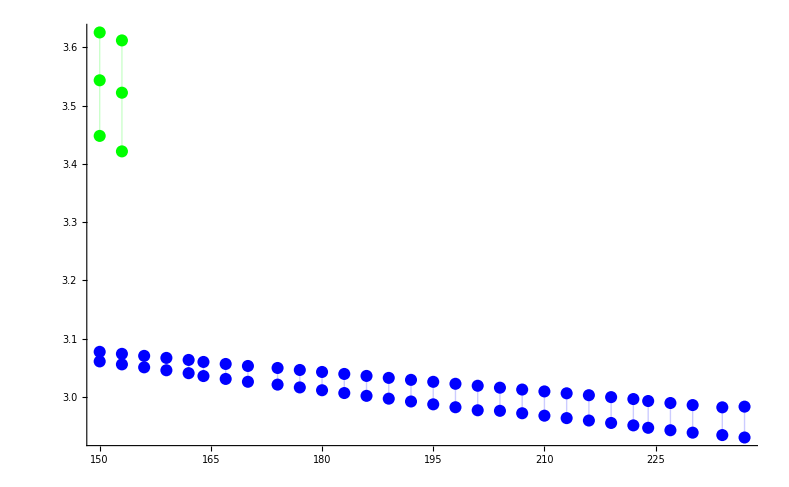

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}}]
```

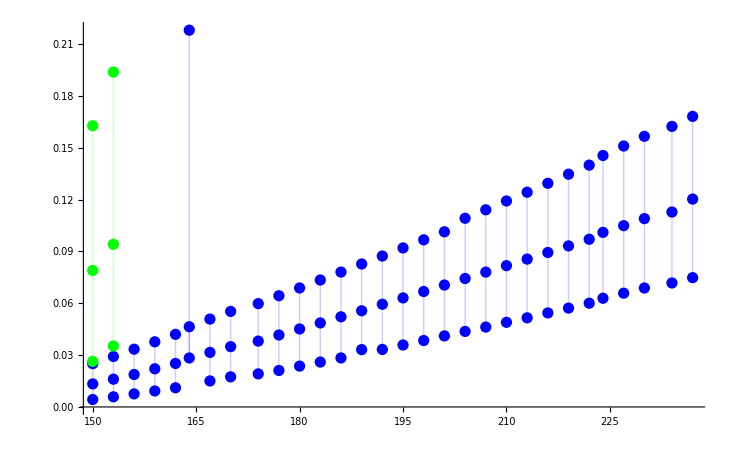

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],Γfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],Γfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],Γfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],Γfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],Γfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],Γfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}}]
```

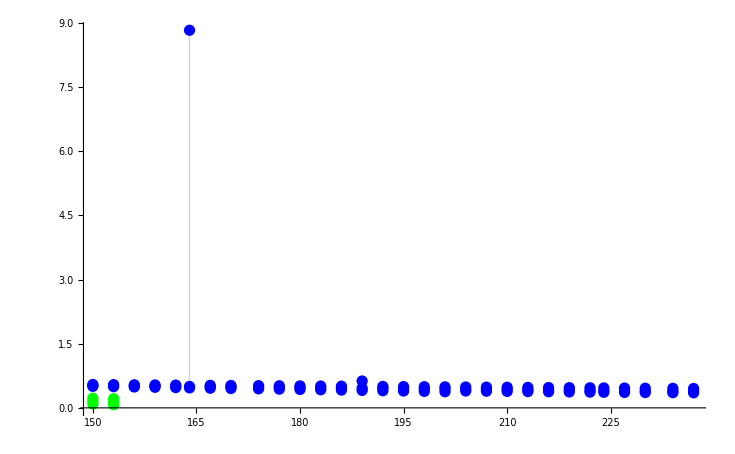

```mathematica
ListPlot[{Transpose[{Tscanc[[;;cc1Tmelt]],areafitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc1Tmelt]],areafitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscanc[[;;cc2Tmelt]],areafitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}}]
```

### Emission Rates

```mathematica
Emfactor=2.356447552594432;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0=ConstantArray[0,ccTcut];
Do[R0[[ii]]={Tscanc[[ii]],Emfactor (areafitcc[[ii,2]]nB[wrfitcc[[ii,2]],Tscanc[[ii]]/1000])/(areafitcc[[ii,1]]nB[wrfitcc[[ii,1]],Tscanc[[ii]]/1000])},{ii,ccTcut}];
```

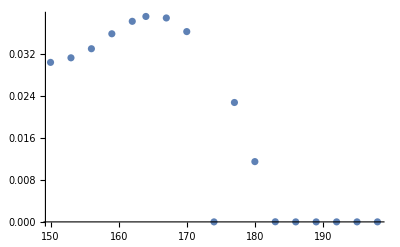

```mathematica
ListPlot[R0]
```

## Bottomonium

```mathematica
Do[bbdata[n]=Import["/Users/davidlafferty/Projects/master/spectraldata/swbbT"<>ToString[n]<>"spectra.dat"];,{n,7}];
Manipulate[ListPlot[bbdata[n],Joined->True],{n,2,7,1}]
```

### Fitting

```mathematica
bbmodel=Range[2,7];
Do[Module[{n=bbmodel[[ii]],maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,bbdatac},
maxx=Max[bbdata[n][[All,1]]];
minx=Min[bbdata[n][[All,1]]];
maxy=Max[bbdata[n][[All,2]]];
maxyx=bbdata[n][[Position[bbdata[n],Max[bbdata[n][[All,2]]]][[1,1]],1]];
maxyi=Position[bbdata[n][[All,1]],maxyx][[1,1]];
maxxy=bbdata[n][[Position[bbdata[n],Max[bbdata[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[bbdata[n],InterpolationOrder->1];
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/20}],First][[All,2]]]];
maxxis=Sort[Table[Position[bbdata[n][[All,1]],Nearest[bbdata[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
maxys=Table[bbdata[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[bbdata[n][[All,2]],Min[bbdata[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];
mins=Append[Prepend[mins,maxxis[[1]]-2 (mins[[1]]-maxxis[[1]])],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])];,
hwhmi=Position[bbdata[n],Nearest[bbdata[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),maxyi+3(maxyi-hwhmi)};];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[bbdata[n],Nearest[bbdata[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
Do[If[Or[2 bbdata[n][[hwhmi[[-i]],2]]≤0.5 maxys[[-i]],2 bbdata[n][[hwhmi[[-i]],2]]≥1.5 maxys[[-i]]],hwhmi[[-i]]=maxxis[[-i]]],{i,Length[hwhmi]-1}];
hwhmi=DeleteCases[maxxis-hwhmi,0];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-bbdata[n][[maxxis[[i]]-hwhmi[[i]],1]]),{i,Length[hwhmi]}];
bbdatac=Range[Length[maxxs]];
Do[bbdatac[[i]]=bbdata[n][[mins[[i]];;mins[[i+1]]]],{i,Length[maxxs]}];
bbmodel[[ii]]=Range[Length[hwhmi]];Do[bbmodel[[ii,i]]=NonlinearModelFit[bbdatac[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w],{i,Length[hwhmi]}];],{ii,Length[bbmodel]}]
```

### Results

```mathematica
wrfitbb=Range[Length[bbmodel]];
Do[wrfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[wrfitbb[[i,ii]]=wr/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[wrfitbb[[i]]]}],{i,Length[wrfitbb]}]

Γfitbb=Range[Length[bbmodel]];
Do[Γfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[Γfitbb[[i,ii]]=Γ/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[Γfitbb[[i]]]}],{i,Length[Γfitbb]}]

constfitbb=Range[Length[bbmodel]];
Do[constfitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[constfitbb[[i,ii]]=const/.bbmodel[[i,ii]]["BestFitParameters"],{ii,Length[constfitbb[[i]]]}],{i,Length[constfitbb]}]

areafitbb=Range[Length[bbmodel]];
Do[areafitbb[[i]]=Range[Length[bbmodel[[i]]]],{i,Length[bbmodel]}];
Do[Do[areafitbb[[i,ii]]=π/2 constfitbb[[i,ii]] Γfitbb[[i,ii]],{ii,Length[areafitbb[[i]]]}],{i,Length[areafitbb]}]
```

```mathematica
Manipulate[Show[{ListPlot[bbdata[i+1],Joined->True],Plot[bbmodel[[i,ii]][x],{x,0.7 wr/.bbmodel[[i,ii]]["BestFitParameters"],1.3 wr/.bbmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wr/.bbmodel[[i,ii]]["BestFitParameters"],Γ/.bbmodel[[i,ii]]["BestFitParameters"],const/.bbmodel[[i,ii]]["BestFitParameters"]],{x,0.7 wr/.bbmodel[[i,ii]]["BestFitParameters"],1.3 wr/.bbmodel[[i,ii]]["BestFitParameters"]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[bbmodel],1},{ii,1,Length[bbmodel[[1]]],1}]
```